```mathematica
data=Import["finalRiseData.tsv"]
```

{{1,0,-7.4501,41.5563,74.9,27.093},{1,100,-7.4499,41.5559,74.4,27.0095},{1,200,-7.4499,41.5558,74.,26.7591},{1,300,-7.4499,41.5558,73.9,26.8425},{1,400,-7.45,41.5559,73.8,27.093},{2,432,-7.4504,41.5519,76.7,32.4365},{1,500,-7.4499,41.5519,76.1,32.52},{1,600,-7.45,41.552,76.,33.0211},{1,700,-7.4502,41.5522,75.9,32.52},{1,800,-7.4504,41.5523,75.8,32.2695},{1,900,-7.4504,41.5524,75.8,33.2717},{1,1000,-7.4505,41.5524,75.8,32.7706},{1,1100,-7.4505,41.5524,75.8,33.1046},{1,1200,-7.4505,41.5524,75.8,32.7706},{1,1300,-7.4506,41.5524,75.8,32.6871},{1,1400,-7.4454,41.5555,79.5,32.2695},{1,1500,-7.4522,41.5591,80.6,32.2695},{1,1600,-7.4526,41.5576,85.7,32.52},{1,1700,-7.4558,41.5587,90.6,32.4365},{1,1800,-7.4563,41.557,88.8,33.3552},{1,1900,-7.4513,41.5582,85.1,32.9376},{1,2000,-7.4513,41.5581,85.2,32.4365},{1,2100,-7.4516,41.5579,85.,32.7706},{1,2200,-7.4517,41.5578,84.9,32.9376},{1,2300,-7.4518,41.5578,84.9,32.6035},{1,2400,-7.4517,41.5578,84.7,33.1882},{1,2500,-7.4517,41.5578,84.7,32.353},{1,2600,-7.4517,41.5578,84.8,32.9376},{1,2700,-7.4515,41.5579,84.6,32.6871},{1,2800,-7.4511,41.5581,84.4,32.9376},{1,2900,-7.4511,41.5581,84.4,32.8541},{1,3000,-7.4508,41.558,84.2,32.9376},{1,3100,-7.4508,41.5579,84.1,33.6893},{1,3200,-7.4508,41.5579,84.1,33.0211},{1,3300,-7.4507,41.5579,84.1,33.1882},{1,3400,-7.4507,41.5579,84.2,33.4387},{1,3500,-7.4506,41.5579,84.2,32.8541},{1,3600,-7.4507,41.5579,84.2,32.9376},{1,3700,-7.4507,41.5578,84.2,33.6893},{1,3800,-7.4506,41.5578,84.1,33.1046},{1,3900,-7.4505,41.5577,84.1,32.8541},{1,4000,-7.4504,41.5576,84.,33.1882},{1,4100,-7.4504,41.5574,84.,33.4387},{1,4200,-7.4503,41.5573,83.9,32.6871},{1,4300,-7.4499,41.5568,84.6,33.1882},{1,4400,-7.4529,41.5532,81.9,33.1046},{1,4500,-7.4545,41.5545,82.3,33.1882},{1,4600,-7.4542,41.5548,83.7,33.5222},{1,4700,-7.4523,41.5553,83.9,33.7728},{1,4800,-7.4522,41.5551,83.8,33.9399},{1,4900,-7.4521,41.5551,83.7,33.5222},{1,5000,-7.4524,41.5536,82.5,33.1882},{1,5100,-7.4525,41.5518,81.5,33.7728},{1,5200,-7.4524,41.5516,81.3,33.7728},{1,5300,-7.4522,41.5514,81.,33.7728},{1,5400,-7.452,41.5514,81.,33.6893},{1,5500,-7.4514,41.5518,81.5,33.5222},{1,5600,-7.4514,41.5519,81.6,33.5222},{1,5700,-7.4513,41.552,81.4,34.1905},{1,5800,-7.4514,41.5521,81.1,33.6893},{1,5900,-7.4513,41.5521,81.,34.274},{1,6000,-7.4512,41.5521,80.8,33.7728},{1,6100,-7.4511,41.5521,80.7,34.274},{1,6200,-7.4511,41.5522,80.6,33.5222},{1,6300,-7.451,41.5523,80.5,34.1069},{1,6400,-7.4509,41.5523,80.2,33.5222},{1,6500,-7.4508,41.5524,80.,34.1905},{1,6600,-7.4507,41.5524,79.7,33.9399},{1,6700,-7.4506,41.5523,79.6,34.8587},{1,6800,-7.4504,41.5519,79.1,34.0234},{1,6900,-7.4503,41.5519,79.,34.6081},{1,7000,-7.4501,41.552,78.9,34.5246},{1,7100,-7.449,41.5512,76.5,35.1093},{1,7200,-7.4491,41.5513,76.4,34.5246},{1,7300,-7.4491,41.5514,76.4,34.8587},{1,7400,-7.4503,41.5533,75.9,35.1928},{1,7500,-7.4504,41.5533,75.9,35.1928},{1,7600,-7.4504,41.5534,75.8,35.4435},{1,7700,-7.4504,41.5534,75.7,34.8587},{1,7800,-7.4505,41.5534,75.6,35.4435},{1,7900,-7.4507,41.5535,75.4,35.4435},{1,8000,-7.4508,41.5535,75.2,35.6105},{1,8100,-7.4514,41.5526,72.6,35.1928},{1,8200,-7.4513,41.5526,72.7,34.8587},{1,8300,-7.4512,41.5525,72.7,35.1928},{1,8400,-7.4511,41.5525,72.7,35.0258},{1,8500,-7.4511,41.5524,72.6,35.4435},{1,8600,-7.4512,41.5525,72.7,35.4435},{1,8700,-7.4513,41.5525,72.6,34.6081},{1,8800,-7.4513,41.5526,72.6,35.3599},{1,8900,-7.4514,41.5526,72.6,35.4435},{1,9000,-7.4517,41.5528,72.7,35.6105},{1,9100,-7.4518,41.5529,72.8,35.6105},{1,9200,-7.4527,41.5537,73.6,35.6941},{1,9300,-7.4527,41.5537,73.6,36.446},{1,9400,-7.4528,41.5538,73.6,35.8612},{1,9500,-7.4529,41.5538,73.5,36.446},{1,9600,-7.4552,41.5554,75.,35.8612},{1,9700,-7.4552,41.5555,74.9,36.1953},{1,9800,-7.4552,41.5556,75.,35.6105},{1,9900,-7.4553,41.5556,75.,36.446},{1,10000,-7.4553,41.5556,75.,36.5295},{1,10100,-7.4557,41.5552,74.9,37.0308},{1,10200,-7.4558,41.5552,74.9,36.9473},{1,10300,-7.4559,41.5552,74.9,36.7802},{1,10400,-7.4559,41.5552,74.9,36.446},{1,10500,-7.456,41.5551,74.9,36.446},{1,10600,-7.4559,41.5549,74.7,36.1953},{1,10700,-7.4559,41.5547,74.6,36.446},{1,10800,-7.4558,41.5546,74.4,36.6966},{1,10900,-7.4558,41.5543,74.1,36.7802},{1,11000,-7.4557,41.5541,73.8,37.0308},{1,11100,-7.4555,41.5538,73.3,37.1979},{1,11200,-7.4555,41.5538,73.2,36.5295},{1,11300,-7.4554,41.5538,73.2,36.6966},{1,11400,-7.4555,41.5538,73.2,37.2815},{1,11500,-7.4555,41.5538,73.2,36.7802},{1,11600,-7.4555,41.5539,73.2,37.5321},{1,11700,-7.4555,41.5539,73.2,37.6157},{1,11800,-7.4555,41.5539,73.2,37.2815},{1,11900,-7.4555,41.5539,73.2,37.365},{1,12000,-7.4554,41.5538,73.1,37.0308},{1,12100,-7.4554,41.5537,73.,38.3677},{1,12200,-7.4553,41.5536,72.9,37.6157},{1,12300,-7.455,41.5533,72.7,37.7828},{1,12400,-7.455,41.5532,72.7,38.0335},{1,12500,-7.4548,41.5531,72.5,37.8664},{1,12600,-7.4547,41.5531,72.5,37.5321},{1,12700,-7.4547,41.5531,72.5,38.2842},{1,12800,-7.4547,41.5531,72.4,37.8664},{1,12900,-7.4546,41.553,72.4,38.8691},{1,13000,-7.4545,41.5529,72.2,38.6184},{1,13100,-7.4545,41.5529,72.2,38.3677},{1,13200,-7.4544,41.5529,72.2,38.2842},{1,13300,-7.4544,41.5529,72.2,37.8664},{1,13400,-7.4536,41.5525,71.6,38.2842},{1,13500,-7.4534,41.5524,71.5,38.9527},{1,13600,-7.4528,41.5521,71.2,38.5348},{1,13700,-7.4509,41.5517,71.,38.2842},{1,13800,-7.4481,41.5509,69.9,38.3677},{1,13900,-7.448,41.5509,69.8,38.702},{1,14000,-7.4476,41.5509,69.8,39.3705},{1,14100,-7.4453,41.5518,69.7,38.702},{1,14200,-7.4468,41.5525,68.,38.8691},{1,14300,-7.4451,41.5525,64.9,39.2034},{1,14400,-7.4437,41.5534,66.5,38.8691},{1,14500,-7.4498,41.5548,73.1,38.5348},{1,14600,-7.4494,41.5554,77.,38.9527},{1,14700,-7.4504,41.5558,75.9,38.6184},{1,14800,-7.4512,41.5563,75.,38.8691},{1,14900,-7.456,41.5578,78.8,38.9527},{1,15000,-7.4546,41.5582,77.5,38.4513},{1,15100,-7.4538,41.5583,77.4,39.3705},{1,15200,-7.4519,41.5571,79.1,39.7884},{1,15300,-7.4515,41.5568,79.4,38.9527},{1,15400,-7.442,41.551,81.2,39.4541},{2,15422,-6.2492,39.7952,-0.6,-21.4576},{1,15500,-6.2491,39.7952,-0.6,-21.4576},{2,15532,-6.249,39.7953,-0.2,-21.5407},{2,15534,-6.2491,39.7952,-0.1,-21.2914},{2,15536,-6.2481,39.795,0.3,-21.5407},{2,15538,-6.2475,39.7949,0.5,-21.2914},{2,15540,-6.2473,39.7947,0.1,-22.0392},{2,15542,-6.2476,39.7947,-0.2,-21.7068},{2,15544,-6.2479,39.7946,-0.3,-21.5407},{2,15548,-6.2483,39.7945,-0.1,-21.5407},{2,15550,-6.2481,39.7944,0.1,-21.6238},{2,15552,-6.2479,39.7946,0.4,-21.7899},{2,15554,-6.2477,39.7948,0.6,-21.5407},{2,15558,-6.2474,39.7959,1.,-21.5407},{2,15560,-6.2478,39.7959,1.6,-21.7899},{2,15566,-6.2484,39.7964,1.9,-21.5407},{2,15572,-6.248,39.7957,2.,-21.2914},{2,15576,-6.2477,39.7955,2.1,-21.7068},{2,15578,-6.2474,39.7953,2.4,-21.873},{2,15580,-6.2473,39.7953,2.6,-22.1222},{2,15582,-6.2471,39.7951,3.,-21.5407},{2,15584,-6.2469,39.795,3.2,-21.4576},{2,15586,-6.2468,39.7948,3.3,-21.7899},{2,15588,-6.2468,39.7948,3.5,-22.2884},{2,15594,-6.2466,39.7943,3.3,-21.2083},{1,15600,-6.2462,39.7936,3.7,-21.5407},{2,15602,-6.2457,39.7931,4.2,-21.7899},{2,15614,-6.2451,39.7915,4.3,-21.2914},{2,15616,-6.2456,39.7912,4.6,-21.4576},{2,15618,-6.2456,39.7906,5.1,-21.2914},{2,15622,-6.2453,39.7897,5.8,-21.2083},{2,15624,-6.2459,39.7893,6.2,-21.2914},{2,15626,-6.2464,39.7887,6.4,-21.2914},{2,15628,-6.2469,39.788,6.6,-21.2914},{2,15630,-6.2466,39.7876,6.9,-22.0392},{2,15632,-6.2459,39.7874,7.2,-21.2914},{2,15636,-6.245,39.7873,8.6,-21.7899},{2,15638,-6.2447,39.7872,9.3,-22.5376},{2,15642,-6.2443,39.7868,10.1,-21.7899},{2,15654,-6.2446,39.7865,11.4,-21.5407},{2,15656,-6.2447,39.7867,11.9,-21.4576},{2,15660,-6.2453,39.7865,13.4,-22.0392},{2,15662,-6.2454,39.7867,14.5,-21.9561},{2,15668,-6.2454,39.7865,15.6,-21.7068},{2,15670,-6.2455,39.7864,16.7,-21.7899},{2,15676,-6.2456,39.7863,18.3,-21.7068},{2,15688,-6.2454,39.7872,18.1,-21.4576},{1,15700,-6.2447,39.7881,18.2,-21.7899},{2,15734,-6.2425,39.7909,18.9,-22.2053},{2,15736,-6.2424,39.7909,19.5,-21.7068},{2,15780,-6.241,39.79,16.6,-22.2884},{2,15782,-6.2408,39.79,16.,-21.7899},{2,15786,-6.2406,39.7898,14.4,-21.5407},{2,15788,-6.2403,39.7906,13.9,-22.3715},{2,15790,-6.2401,39.7917,13.2,-21.7899},{2,15792,-6.2402,39.7922,12.7,-22.2053},{1,15800,-6.2403,39.7923,12.4,-22.2053},{2,15854,-6.2423,39.7945,12.5,-22.7868},{2,15876,-6.2428,39.7968,11.8,-22.0392},{2,15878,-6.243,39.7969,11.4,-22.5376},{2,15880,-6.2433,39.797,10.9,-22.7038},{2,15882,-6.2432,39.7975,10.5,-22.4545},{2,15884,-6.2432,39.7978,10.,-22.0392},{1,15900,-6.2425,39.7995,8.9,-21.9561},{2,15922,-6.2449,39.7992,7.,-22.7038},{2,15926,-6.2448,39.7987,6.6,-22.7868},{2,15928,-6.2449,39.799,6.3,-22.7038},{2,15930,-6.2449,39.7996,6.1,-22.7038},{2,15934,-6.2444,39.8012,5.9,-22.4545},{2,15936,-6.244,39.8016,5.7,-22.7868},{2,15938,-6.2436,39.802,5.5,-22.7038},{2,15962,-6.2432,39.8029,5.,-22.2053},{2,15964,-6.2432,39.8041,4.7,-22.4545},{2,15966,-6.243,39.8049,4.5,-22.5376},{2,15968,-6.2428,39.8051,4.3,-22.7038},{2,15982,-6.2428,39.805,3.5,-22.2053},{2,15984,-6.243,39.8051,3.3,-22.4545},{2,15986,-6.2432,39.8051,3.,-22.4545},{2,15988,-6.2433,39.8047,2.7,-22.7038},{2,15990,-6.2433,39.8039,2.4,-22.4545},{2,15992,-6.2436,39.803,2.2,-22.7038},{2,15994,-6.2436,39.803,1.9,-22.4545},{2,15998,-6.244,39.8019,1.8,-22.0392},{1,16000,-6.2442,39.8017,1.8,-22.2053},{2,16002,-6.2443,39.8012,1.9,-22.5376},{2,16016,-6.2444,39.8014,2.,-22.2053},{1,16100,-6.2445,39.8014,2.,-22.2053},{2,16124,-6.2445,39.8013,1.9,-22.4545},{2,16138,-6.2445,39.8009,1.1,-21.7899},{2,16152,-6.2441,39.8003,1.,-22.0392},{2,16154,-6.2439,39.8004,0.7,-22.0392},{2,16156,-6.2438,39.8006,0.6,-22.2053},{2,16158,-6.2439,39.8008,0.2,-22.4545},{2,16160,-6.244,39.8006,-0.2,-22.7038},{2,16162,-6.2442,39.801,-0.8,-22.0392},{2,16164,-6.2442,39.8004,-1.5,-22.5376},{2,16166,-6.244,39.8001,-2.,-22.2884},{2,16168,-6.2439,39.7998,-3.1,-22.5376},{2,16170,-6.2442,39.8004,-4.2,-23.1191},{2,16172,-6.2448,39.8009,-4.8,-22.4545},{2,16174,-6.2453,39.8007,-5.4,-22.4545},{2,16176,-6.2454,39.799,-6.,-22.2884},{2,16178,-6.2458,39.7981,-6.5,-22.4545},{2,16180,-6.2462,39.7971,-7.3,-22.7038},{2,16182,-6.2464,39.7964,-7.6,-22.5376},{2,16184,-6.2466,39.7964,-8.,-22.4545},{2,16188,-6.2474,39.7963,-8.1,-22.7868},{2,16190,-6.2482,39.7964,-8.5,-22.5376},{2,16194,-6.249,39.7962,-9.,-22.2884},{2,16196,-6.2493,39.7958,-9.8,-22.6207},{2,16198,-6.2495,39.7956,-10.8,-22.4545},{1,16200,-6.2497,39.796,-11.9,-22.8699},{2,16202,-6.2501,39.7961,-12.8,-22.2053},{2,16204,-6.2506,39.7958,-13.7,-22.5376},{2,16206,-6.2508,39.7949,-14.4,-22.2053},{2,16214,-6.25,39.7956,-15.,-22.5376},{2,16240,-6.2502,39.794,-18.7,-22.2053},{2,16244,-6.2508,39.7934,-19.8,-22.8699},{1,16300,-6.2494,39.7952,-19.1,-22.5376},{1,16400,-6.2472,39.7961,-18.9,-22.8699},{1,16500,-6.2465,39.7947,-18.9,-22.2053},{1,16600,-6.2455,39.7922,-17.4,-22.5376},{1,16700,-6.2449,39.7937,-19.1,-22.2053},{1,16800,-6.2463,39.797,-19.7,-23.4514},{1,16900,-6.2462,39.797,-19.8,-22.2053},{1,17000,-6.246,39.797,-19.7,-22.7868},{2,17036,-6.2471,39.7955,-17.7,-22.7038},{2,17038,-6.2471,39.7958,-17.1,-23.0361},{1,17100,-6.2452,39.7957,-14.2,-22.7868},{1,17200,-6.2451,39.7957,-14.2,-22.6207},{1,17300,-6.2451,39.7957,-14.2,-22.6207},{2,17350,-6.2442,39.7953,-15.5,-22.1222},{2,17366,-6.2416,39.7946,-16.5,-22.3715},{2,17370,-6.2394,39.7948,-15.9,-21.9561},{2,17372,-6.2384,39.7952,-14.9,-22.2884},{2,17374,-6.2368,39.7953,-13.8,-22.0392},{2,17376,-6.2357,39.7952,-13.2,-22.2884},{1,17400,-6.2354,39.7955,-13.7,-22.7868},{1,17500,-6.2362,39.7958,-13.8,-22.7038},{1,17600,-6.2387,39.8121,-15.,-23.9498},{2,17646,-6.2383,39.8123,-14.1,-23.1191},{2,17648,-6.2377,39.8123,-13.4,-23.1191},{2,17668,-6.2192,39.8241,-13.3,-21.9561},{2,17672,-6.2081,39.8246,-14.2,-23.0361},{2,17682,-6.1968,39.8317,-13.3,-22.8699},{1,17700,-6.1972,39.8326,-12.8,-22.2884},{2,17736,-6.0547,39.8356,-12.7,-21.4576},{2,17748,-6.0065,39.8414,-12.5,-19.0479},{2,17750,-5.9988,39.8432,-11.6,-18.2168},{2,17752,-5.9919,39.8449,-11.2,-18.1337},{2,17754,-5.9859,39.8471,-10.8,-18.1337},{2,17756,-5.9811,39.8501,-10.4,-18.7155},{2,17770,-5.9872,39.888,-9.7,-18.4662},{2,17774,-5.9907,39.8998,-9.2,-18.6324},{2,17782,-5.9963,39.9195,-8.3,-19.0479},{2,17788,-5.9976,39.9258,-7.6,-19.4634},{1,17800,-5.9977,39.9261,-7.6,-18.7986},{2,17892,-5.9973,39.9262,-8.1,-19.8789},{2,17894,-5.9971,39.927,-8.4,-19.131},{2,17898,-5.9976,39.932,-9.1,-19.0479},{1,17900,-5.9981,39.9361,-9.5,-19.0479},{2,17902,-5.9988,39.9411,-9.8,-18.2168},{2,17942,-6.099,40.0499,-12.7,-19.0479},{1,18000,-6.1039,40.0525,-14.3,-20.2944},{2,18032,-6.2323,40.1233,-14.3,-19.131},{2,18038,-6.263,40.1351,-13.2,-19.0479},{2,18040,-6.2723,40.1385,-12.8,-19.0479},{1,18100,-6.4222,40.1819,-10.1,-19.131},{2,18116,-6.4992,40.2043,-10.,-18.9648},{2,18134,-6.5758,40.2285,-9.2,-20.2944},{2,18138,-6.5904,40.2322,-9.,-19.7127},{2,18140,-6.5973,40.234,-8.6,-19.962},{2,18172,-6.7242,40.2712,-9.1,-20.2944},{2,18186,-6.7612,40.2823,-10.,-19.7127},{2,18188,-6.768,40.2844,-10.4,-19.4634},{1,18200,-6.8176,40.299,-11.2,-19.2972},{2,18258,-6.9295,40.331,-10.9,-20.2944},{1,18300,-7.0998,40.3803,-10.4,-20.2944},{2,18314,-7.1346,40.3955,-9.7,-20.2944},{2,18316,-7.1349,40.4002,-9.1,-20.5436},{2,18318,-7.1346,40.4061,-8.5,-19.8789},{2,18320,-7.1345,40.4125,-8.1,-19.7127},{2,18322,-7.1347,40.4187,-7.3,-19.8789},{2,18336,-7.1439,40.4674,-6.7,-18.4662},{2,18338,-7.1465,40.4745,-6.3,-18.8817},{2,18340,-7.1489,40.4818,-6.,-19.5465},{2,18342,-7.1506,40.4892,-6.4,-18.7986},{2,18344,-7.1518,40.4966,-7.3,-19.7127},{2,18350,-7.1513,40.518,-8.,-19.7127},{2,18352,-7.1509,40.525,-8.3,-19.5465},{2,18354,-7.1506,40.5323,-8.6,-19.5465},{2,18356,-7.1502,40.5394,-9.2,-19.5465},{2,18370,-7.1488,40.5912,-10.,-20.5436},{2,18380,-7.1486,40.6282,-9.8,-19.6296},{2,18382,-7.1484,40.6355,-9.2,-20.0451},{2,18384,-7.1483,40.6426,-8.8,-20.1282},{2,18388,-7.1479,40.6566,-9.1,-20.1282},{2,18390,-7.1473,40.6639,-8.8,-19.2141},{2,18392,-7.1469,40.6714,-8.2,-19.2141},{2,18394,-7.1466,40.6786,-7.7,-18.7986},{2,18396,-7.1466,40.6856,-7.,-17.8013},{2,18398,-7.1465,40.6925,-6.2,-16.8039},{1,18400,-7.1469,40.6997,-5.3,-15.6401},{2,18402,-7.1471,40.7071,-4.5,-14.6425},{2,18404,-7.1472,40.7147,-3.4,-13.4785},{2,18406,-7.1476,40.7224,-2.5,-11.3165},{2,18408,-7.1481,40.7298,-1.4,-9.48671},{2,18410,-7.1483,40.7372,-0.8,-8.07257},{2,18412,-7.1481,40.7446,0.3,-6.15902},{2,18414,-7.1481,40.7517,1.9,-4.99408},{2,18416,-7.1482,40.7586,3.3,-3.82901},{2,18418,-7.1479,40.7654,5.3,-2.08116},{2,18420,-7.1477,40.7724,6.6,-0.499516},{2,18422,-7.1475,40.7794,8.3,0.915841},{2,18424,-7.1475,40.7863,10.1,1.66523},{2,18426,-7.1473,40.7933,11.8,2.9976},{2,18428,-7.1471,40.8002,13.8,3.66385},{2,18430,-7.1469,40.8069,15.4,5.07977},{2,18432,-7.1468,40.8133,16.7,5.82945},{2,18434,-7.1466,40.819,17.6,6.6625},{2,18436,-7.1467,40.8243,18.9,7.99551},{2,18438,-7.1467,40.8296,19.9,8.41211},{2,18440,-7.1466,40.8345,21.8,9.66202},{2,18442,-7.1468,40.8396,23.4,10.4954},{2,18444,-7.1469,40.845,24.4,11.0788},{2,18446,-7.1471,40.8504,25.5,12.1623},{2,18448,-7.147,40.8558,26.5,13.5794},{2,18452,-7.1476,40.867,28.4,14.6631},{2,18480,-7.1466,40.9491,38.7,27.8442},{2,18482,-7.1466,40.9547,40.6,28.5121},{2,18484,-7.1466,40.9605,42.,29.0965},{1,18500,-7.1465,41.0087,46.3,33.1882},{1,18600,-7.3328,41.1412,54.9,39.2869},{1,18700,-7.4866,41.3301,48.5,37.6992},{1,18800,-7.595,41.5151,56.,44.1351},{1,18900,-7.4539,41.5572,55.9,46.56},{1,19000,-7.4565,41.5539,62.2,48.6509},{1,19100,-7.4533,41.5528,66.2,49.3201},{1,19200,-7.4535,41.5531,65.9,48.9018},{1,19300,-7.4535,41.5531,65.8,48.5673},{1,19400,-7.4535,41.5531,65.7,49.1528},{1,19500,-7.4535,41.5532,65.8,49.0691},{1,19600,-7.4534,41.5531,65.9,49.0691},{1,19700,-7.4534,41.5531,65.9,48.9855},{1,19800,-7.4534,41.5531,66.,49.0691},{1,19900,-7.4534,41.5531,66.2,47.8981},{1,20000,-7.4534,41.553,66.4,48.8182},{1,20100,-7.4535,41.5534,67.1,48.5673},{1,20200,-7.4535,41.5535,67.1,48.0654},{1,20300,-7.4536,41.5535,67.1,49.1528},{1,20400,-7.4536,41.5536,67.2,48.8182},{1,20500,-7.4538,41.5539,67.7,48.5673},{1,20600,-7.4538,41.5539,67.7,48.5673},{1,20700,-7.4538,41.5539,67.8,48.6509},{1,20800,-7.4538,41.5539,67.8,48.6509},{1,20900,-7.4538,41.5539,67.8,48.5673},{1,21000,-7.4538,41.5539,67.8,49.2364},{1,21100,-7.4538,41.5539,67.8,48.8182},{1,21200,-7.4538,41.554,67.9,49.1528},{1,21300,-7.4537,41.5541,67.9,48.9018},{1,21400,-7.4535,41.5542,68.,49.7383},{1,21500,-7.4535,41.5543,68.1,49.1528},{1,21600,-7.4535,41.5543,68.1,49.6547},{1,21700,-7.4534,41.5543,68.2,48.8182},{1,21800,-7.4532,41.5543,68.2,48.6509},{1,21900,-7.4532,41.5543,68.3,49.2364},{1,22000,-7.4531,41.5543,68.3,49.1528},{1,22100,-7.4531,41.5542,68.3,48.9018},{1,22200,-7.453,41.5542,68.3,48.7346},{1,22300,-7.453,41.5542,68.3,49.4874},{1,22400,-7.4529,41.5541,68.3,48.7346},{1,22500,-7.4529,41.554,68.3,49.7383},{1,22600,-7.4529,41.554,68.3,49.7383},{1,22700,-7.4529,41.554,68.3,49.2364},{1,22800,-7.4529,41.5539,68.3,49.7383},{1,22900,-7.4529,41.5538,68.3,49.4874},{1,23000,-7.453,41.5537,68.1,49.7383},{1,23100,-7.453,41.5537,68.1,49.571},{1,23200,-7.453,41.5536,68.2,49.1528},{1,23300,-7.453,41.5536,68.4,49.3201},{1,23400,-7.4542,41.552,69.1,49.0691},{1,23500,-7.4551,41.5526,69.5,48.9855},{1,23600,-7.4552,41.5528,69.9,49.4874},{1,23700,-7.4539,41.5528,69.8,50.073},{1,23800,-7.4532,41.553,69.6,50.3239},{1,23900,-7.453,41.5532,69.6,49.7383},{1,24000,-7.4529,41.5533,69.7,49.3201},{1,24100,-7.4529,41.5533,69.8,50.073},{1,24200,-7.453,41.5533,69.9,49.9057},{1,24300,-7.4529,41.5534,70.,50.073},{1,24400,-7.4529,41.5533,70.1,50.073},{1,24500,-7.4529,41.5533,70.4,49.9057},{1,24600,-7.4529,41.5534,70.6,50.4913},{1,24700,-7.4529,41.5535,70.8,50.4913},{1,24800,-7.4528,41.5535,70.9,50.073},{1,24900,-7.4527,41.5535,70.9,50.073},{1,25000,-7.4527,41.5536,71.,50.9932},{1,25100,-7.4527,41.5536,71.1,50.1566},{1,25200,-7.4528,41.5538,71.4,49.9057},{1,25300,-7.4528,41.5537,71.4,50.073},{1,25400,-7.4528,41.5537,71.4,49.571},{1,25500,-7.4528,41.5536,71.5,49.9057},{1,25600,-7.4528,41.5536,71.5,50.073},{1,25700,-7.4528,41.5537,71.6,49.6547},{1,25800,-7.4528,41.5536,71.7,49.6547},{1,25900,-7.4528,41.5535,71.8,49.9057},{1,26000,-7.4527,41.5535,71.9,49.9057},{1,26100,-7.4529,41.5532,72.2,50.1566},{1,26200,-7.4529,41.5531,72.3,49.4037},{1,26300,-7.4529,41.553,72.4,50.073},{1,26400,-7.4532,41.5529,72.8,49.571},{1,26500,-7.4532,41.553,72.2,50.1566},{1,26600,-7.4566,41.5507,70.7,49.6547},{1,26700,-7.4495,41.553,75.5,50.4076},{1,26800,-7.4497,41.553,75.5,49.9057},{1,26900,-7.4497,41.553,75.6,50.1566},{1,27000,-7.4496,41.553,75.5,50.6586},{1,27100,-7.4495,41.5529,75.5,50.9096},{1,27200,-7.4493,41.5527,75.4,50.1566},{1,27300,-7.4491,41.5526,75.5,50.4913},{1,27400,-7.4493,41.5526,75.5,50.1566},{1,27500,-7.4522,41.5535,77.9,50.4913},{1,27600,-7.4523,41.5535,78.1,50.7422},{1,27700,-7.4521,41.5536,78.3,50.1566},{1,27800,-7.452,41.5536,78.4,49.6547},{1,27900,-7.4522,41.5534,78.4,50.1566},{1,28000,-7.4521,41.5534,78.4,50.4076},{1,28100,-7.4519,41.5534,78.3,50.2403},{1,28200,-7.4518,41.5533,78.2,50.9932},{1,28300,-7.4517,41.5533,78.,51.2442},{1,28400,-7.4515,41.5534,77.7,50.9932},{1,28500,-7.4503,41.5549,78.8,50.4076},{1,28600,-7.4503,41.5549,78.8,50.7422},{1,28700,-7.4503,41.5549,78.8,50.5749},{1,28800,-7.4503,41.5549,78.7,50.7422},{1,28900,-7.4503,41.5549,78.6,50.9932},{1,29000,-7.4503,41.5549,78.5,50.2403},{1,29100,-7.4504,41.5549,78.5,51.2442},{1,29200,-7.4504,41.5549,78.6,50.4913},{1,29300,-7.4504,41.5549,78.5,51.3279},{1,29400,-7.4506,41.5549,78.6,51.4115},{1,29500,-7.4506,41.5549,78.6,50.7422},{1,29600,-7.4507,41.5549,78.5,51.2442},{1,29700,-7.4508,41.5548,78.5,51.5789},{1,29800,-7.4508,41.5548,78.4,51.8299},{1,29900,-7.4513,41.5546,78.1,51.5789},{1,30000,-7.452,41.5544,77.7,51.8299},{1,30100,-7.4521,41.5544,77.6,51.8299},{1,30200,-7.4521,41.5544,77.6,51.5789},{1,30300,-7.4518,41.5544,77.6,52.4993},{1,30400,-7.4518,41.5545,77.6,52.4156},{1,30500,-7.4516,41.5544,77.9,51.6625},{1,30600,-7.4514,41.5543,78.2,52.0809},{1,30700,-7.4514,41.5544,78.3,51.5789},{1,30800,-7.4514,41.5544,78.3,51.5789},{1,30900,-7.4514,41.5544,78.4,52.0809},{1,31000,-7.4515,41.5545,78.5,51.8299},{1,31100,-7.4515,41.5545,78.5,51.8299},{1,31200,-7.4515,41.5545,78.5,51.9136},{1,31300,-7.4515,41.5544,78.4,51.4115},{1,31400,-7.4515,41.5544,78.3,51.4115},{1,31500,-7.4516,41.5544,78.3,51.6625},{1,31600,-7.4517,41.5543,78.2,51.5789},{1,31700,-7.4518,41.5543,78.1,52.1646},{1,31800,-7.4518,41.5542,78.2,52.1646},{1,31900,-7.4518,41.5542,78.2,52.2482},{1,32000,-7.4518,41.5542,78.2,52.2482},{1,32100,-7.4519,41.5542,78.1,52.7503},{1,32200,-7.4519,41.5542,78.1,52.4993},{1,32300,-7.4521,41.5539,77.8,52.7503},{1,32400,-7.4522,41.5539,77.8,53.085},{1,32500,-7.4526,41.5538,77.4,52.6666},{1,32600,-7.4526,41.5537,77.3,53.0013},{1,32700,-7.4527,41.5537,77.3,52.4156},{1,32800,-7.4528,41.5537,77.2,52.1646},{1,32900,-7.4528,41.5537,77.2,52.2482},{1,33000,-7.453,41.5536,77.,52.7503},{1,33100,-7.453,41.5536,77.,52.6666},{1,33200,-7.4529,41.5536,76.9,51.9136},{1,33300,-7.4529,41.5536,76.9,52.2482},{1,33400,-7.4528,41.5536,76.8,52.4993},{1,33500,-7.4527,41.5536,76.8,52.7503},{1,33600,-7.4527,41.5535,76.7,52.2482},{1,33700,-7.4527,41.5536,76.7,52.4156},{1,33800,-7.4526,41.5535,76.6,52.5829},{1,33900,-7.4525,41.5535,76.5,52.4993},{1,34000,-7.457,41.5548,78.4,52.834},{1,34100,-7.4569,41.5535,78.9,52.4993},{1,34200,-7.4565,41.5533,78.9,52.4156},{1,34300,-7.4564,41.5534,78.9,53.4197},{1,34400,-7.4561,41.5534,79.,52.7503},{1,34500,-7.456,41.5535,78.9,53.085},{1,34600,-7.4557,41.5535,78.9,53.2524},{1,34700,-7.4554,41.5536,78.8,53.0013},{1,34800,-7.4551,41.5536,78.8,53.085},{1,34900,-7.4549,41.5535,78.7,52.4993},{1,35000,-7.4547,41.5535,78.6,52.4156},{1,35100,-7.4545,41.5535,78.7,53.5871},{1,35200,-7.4543,41.5535,78.7,53.3361},{1,35300,-7.4542,41.5534,78.7,53.0013},{1,35400,-7.4541,41.5533,78.7,52.4993},{1,35500,-7.4539,41.5533,78.7,52.834},{1,35600,-7.4538,41.5533,78.7,53.0013},{1,35700,-7.4537,41.5533,78.7,53.5871},{1,35800,-7.4536,41.5533,78.7,53.2524},{1,35900,-7.4535,41.5532,78.6,53.8382},{1,36000,-7.4535,41.5532,78.5,53.3361},{1,36100,-7.4535,41.5532,78.5,53.9218},{1,36200,-7.4535,41.5532,78.4,53.5034},{1,36300,-7.4536,41.5532,78.2,53.2524},{1,36400,-7.4536,41.5531,78.1,54.0892},{1,36500,-7.4537,41.5527,78.1,53.8382},{1,36600,-7.4537,41.5526,78.,53.6708},{1,36700,-7.4537,41.5525,77.9,53.8382},{1,36800,-7.4536,41.5523,77.7,53.5871},{1,36900,-7.4536,41.5522,77.6,53.5034},{1,37000,-7.4537,41.5521,77.6,53.5034},{1,37100,-7.4537,41.5521,77.5,53.0013},{1,37200,-7.4537,41.5522,77.4,54.1729},{1,37300,-7.4536,41.5522,77.4,54.0892},{1,37400,-7.4532,41.5523,76.9,53.5034},{1,37500,-7.4532,41.5524,76.8,53.3361},{1,37600,-7.4532,41.5524,76.8,54.1729},{1,37700,-7.4531,41.5523,76.7,53.7545},{1,37800,-7.4531,41.5523,76.6,53.7545},{1,37900,-7.4531,41.5523,76.5,53.5034},{1,38000,-7.4531,41.5522,76.4,53.3361},{1,38100,-7.453,41.5522,76.4,53.3361},{1,38200,-7.453,41.5523,76.4,53.3361},{1,38300,-7.453,41.5523,76.4,53.8382},{1,38400,-7.453,41.5523,76.3,54.1729},{1,38500,-7.453,41.5523,76.3,53.8382},{1,38600,-7.453,41.5523,76.3,53.5871},{1,38700,-7.453,41.5523,76.3,54.0892},{1,38800,-7.453,41.5524,76.2,54.3403},{1,38900,-7.453,41.5524,76.2,53.7545},{1,39000,-7.453,41.5523,75.9,54.0055},{1,39100,-7.453,41.5523,75.8,53.5034},{1,39200,-7.4529,41.5522,75.8,54.0055},{1,39300,-7.4529,41.5523,75.8,53.7545},{1,39400,-7.4529,41.5523,75.8,53.8382},{1,39500,-7.4529,41.5524,75.8,54.0055},{1,39600,-7.4522,41.5533,74.9,53.2524},{1,39700,-7.4518,41.5537,73.7,54.3403},{1,39800,-7.4517,41.5545,72.9,53.7545},{1,39900,-7.4517,41.5545,72.9,53.5871},{1,40000,-7.4517,41.5545,73.,54.1729},{1,40100,-7.4517,41.5545,73.1,53.5871},{1,40200,-7.4487,41.5523,73.8,53.8382},{1,40300,-7.4533,41.5527,69.7,54.0055},{1,40400,-7.4532,41.5528,69.6,54.424},{1,40500,-7.4531,41.5529,70.1,53.7545},{1,40600,-7.4529,41.5532,70.1,53.1687},{1,40700,-7.4529,41.5531,70.1,53.7545},{1,40800,-7.4529,41.5532,70.1,53.7545},{1,40900,-7.4529,41.5532,70.1,53.5871},{1,41000,-7.4528,41.5534,70.1,53.5871},{1,41100,-7.4527,41.5534,70.1,54.0055},{1,41200,-7.4526,41.5533,70.1,54.0055},{1,41300,-7.4524,41.5533,70.1,53.7545},{1,41400,-7.4523,41.5534,70.1,54.5914},{1,41500,-7.4523,41.5534,70.2,54.424},{1,41600,-7.4522,41.5534,70.3,54.0055},{1,41700,-7.4521,41.5534,70.4,54.3403},{1,41800,-7.452,41.5534,70.4,54.0892},{1,41900,-7.4519,41.5534,70.3,54.0892},{1,42000,-7.4519,41.5534,70.3,54.1729},{1,42100,-7.4518,41.5535,70.3,55.1772},{1,42200,-7.4517,41.5535,70.2,54.6751},{1,42300,-7.4516,41.5535,70.2,55.1772},{1,42400,-7.4516,41.5534,70.1,54.9261},{1,42500,-7.4516,41.5534,69.9,54.424},{1,42600,-7.4516,41.5534,69.9,54.3403},{1,42700,-7.4516,41.5534,69.8,54.9261},{1,42800,-7.4516,41.5534,69.8,54.424},{1,42900,-7.4516,41.5535,69.7,54.3403},{1,43000,-7.4516,41.5535,69.3,54.9261},{1,43100,-7.4516,41.5532,69.2,55.512},{1,43200,-7.4515,41.5532,69.3,55.1772},{1,43300,-7.4516,41.5531,68.9,55.2609},{1,43400,-7.4516,41.5532,68.9,55.2609},{1,43500,-7.4517,41.5533,68.5,54.9261},{1,43600,-7.4517,41.5533,68.6,55.0935},{1,43700,-7.4518,41.5533,68.5,55.512},{1,43800,-7.4517,41.5533,68.5,55.4283},{1,43900,-7.4517,41.5533,68.6,55.6794},{1,44000,-7.4516,41.5534,68.6,54.8424},{1,44100,-7.4517,41.5534,68.6,55.2609},{1,44200,-7.4516,41.5534,68.6,55.512},{1,44300,-7.4515,41.5534,68.7,55.4283},{1,44400,-7.4514,41.5534,68.7,54.8424},{1,44500,-7.4513,41.5535,68.7,55.4283},{1,44600,-7.4513,41.5536,68.7,55.4283},{1,44700,-7.4513,41.5536,68.7,55.512},{1,44800,-7.4513,41.5536,68.6,55.4283},{1,44900,-7.4513,41.5536,68.6,55.2609},{1,45000,-7.4514,41.5536,68.6,55.512},{1,45100,-7.4514,41.5535,68.6,55.6794},{1,45200,-7.4514,41.5535,68.6,55.4283}}

```mathematica
foo=data[[All,3;; 5]]
```

{{-7.4501,41.5563,74.9},{-7.4499,41.5559,74.4},{-7.4499,41.5558,74.},{-7.4499,41.5558,73.9},{-7.45,41.5559,73.8},{-7.4504,41.5519,76.7},{-7.4499,41.5519,76.1},{-7.45,41.552,76.},{-7.4502,41.5522,75.9},{-7.4504,41.5523,75.8},{-7.4504,41.5524,75.8},{-7.4505,41.5524,75.8},{-7.4505,41.5524,75.8},{-7.4505,41.5524,75.8},{-7.4506,41.5524,75.8},{-7.4454,41.5555,79.5},{-7.4522,41.5591,80.6},{-7.4526,41.5576,85.7},{-7.4558,41.5587,90.6},{-7.4563,41.557,88.8},{-7.4513,41.5582,85.1},{-7.4513,41.5581,85.2},{-7.4516,41.5579,85.},{-7.4517,41.5578,84.9},{-7.4518,41.5578,84.9},{-7.4517,41.5578,84.7},{-7.4517,41.5578,84.7},{-7.4517,41.5578,84.8},{-7.4515,41.5579,84.6},{-7.4511,41.5581,84.4},{-7.4511,41.5581,84.4},{-7.4508,41.558,84.2},{-7.4508,41.5579,84.1},{-7.4508,41.5579,84.1},{-7.4507,41.5579,84.1},{-7.4507,41.5579,84.2},{-7.4506,41.5579,84.2},{-7.4507,41.5579,84.2},{-7.4507,41.5578,84.2},{-7.4506,41.5578,84.1},{-7.4505,41.5577,84.1},{-7.4504,41.5576,84.},{-7.4504,41.5574,84.},{-7.4503,41.5573,83.9},{-7.4499,41.5568,84.6},{-7.4529,41.5532,81.9},{-7.4545,41.5545,82.3},{-7.4542,41.5548,83.7},{-7.4523,41.5553,83.9},{-7.4522,41.5551,83.8},{-7.4521,41.5551,83.7},{-7.4524,41.5536,82.5},{-7.4525,41.5518,81.5},{-7.4524,41.5516,81.3},{-7.4522,41.5514,81.},{-7.452,41.5514,81.},{-7.4514,41.5518,81.5},{-7.4514,41.5519,81.6},{-7.4513,41.552,81.4},{-7.4514,41.5521,81.1},{-7.4513,41.5521,81.},{-7.4512,41.5521,80.8},{-7.4511,41.5521,80.7},{-7.4511,41.5522,80.6},{-7.451,41.5523,80.5},{-7.4509,41.5523,80.2},{-7.4508,41.5524,80.},{-7.4507,41.5524,79.7},{-7.4506,41.5523,79.6},{-7.4504,41.5519,79.1},{-7.4503,41.5519,79.},{-7.4501,41.552,78.9},{-7.449,41.5512,76.5},{-7.4491,41.5513,76.4},{-7.4491,41.5514,76.4},{-7.4503,41.5533,75.9},{-7.4504,41.5533,75.9},{-7.4504,41.5534,75.8},{-7.4504,41.5534,75.7},{-7.4505,41.5534,75.6},{-7.4507,41.5535,75.4},{-7.4508,41.5535,75.2},{-7.4514,41.5526,72.6},{-7.4513,41.5526,72.7},{-7.4512,41.5525,72.7},{-7.4511,41.5525,72.7},{-7.4511,41.5524,72.6},{-7.4512,41.5525,72.7},{-7.4513,41.5525,72.6},{-7.4513,41.5526,72.6},{-7.4514,41.5526,72.6},{-7.4517,41.5528,72.7},{-7.4518,41.5529,72.8},{-7.4527,41.5537,73.6},{-7.4527,41.5537,73.6},{-7.4528,41.5538,73.6},{-7.4529,41.5538,73.5},{-7.4552,41.5554,75.},{-7.4552,41.5555,74.9},{-7.4552,41.5556,75.},{-7.4553,41.5556,75.},{-7.4553,41.5556,75.},{-7.4557,41.5552,74.9},{-7.4558,41.5552,74.9},{-7.4559,41.5552,74.9},{-7.4559,41.5552,74.9},{-7.456,41.5551,74.9},{-7.4559,41.5549,74.7},{-7.4559,41.5547,74.6},{-7.4558,41.5546,74.4},{-7.4558,41.5543,74.1},{-7.4557,41.5541,73.8},{-7.4555,41.5538,73.3},{-7.4555,41.5538,73.2},{-7.4554,41.5538,73.2},{-7.4555,41.5538,73.2},{-7.4555,41.5538,73.2},{-7.4555,41.5539,73.2},{-7.4555,41.5539,73.2},{-7.4555,41.5539,73.2},{-7.4555,41.5539,73.2},{-7.4554,41.5538,73.1},{-7.4554,41.5537,73.},{-7.4553,41.5536,72.9},{-7.455,41.5533,72.7},{-7.455,41.5532,72.7},{-7.4548,41.5531,72.5},{-7.4547,41.5531,72.5},{-7.4547,41.5531,72.5},{-7.4547,41.5531,72.4},{-7.4546,41.553,72.4},{-7.4545,41.5529,72.2},{-7.4545,41.5529,72.2},{-7.4544,41.5529,72.2},{-7.4544,41.5529,72.2},{-7.4536,41.5525,71.6},{-7.4534,41.5524,71.5},{-7.4528,41.5521,71.2},{-7.4509,41.5517,71.},{-7.4481,41.5509,69.9},{-7.448,41.5509,69.8},{-7.4476,41.5509,69.8},{-7.4453,41.5518,69.7},{-7.4468,41.5525,68.},{-7.4451,41.5525,64.9},{-7.4437,41.5534,66.5},{-7.4498,41.5548,73.1},{-7.4494,41.5554,77.},{-7.4504,41.5558,75.9},{-7.4512,41.5563,75.},{-7.456,41.5578,78.8},{-7.4546,41.5582,77.5},{-7.4538,41.5583,77.4},{-7.4519,41.5571,79.1},{-7.4515,41.5568,79.4},{-7.442,41.551,81.2},{-6.2492,39.7952,-0.6},{-6.2491,39.7952,-0.6},{-6.249,39.7953,-0.2},{-6.2491,39.7952,-0.1},{-6.2481,39.795,0.3},{-6.2475,39.7949,0.5},{-6.2473,39.7947,0.1},{-6.2476,39.7947,-0.2},{-6.2479,39.7946,-0.3},{-6.2483,39.7945,-0.1},{-6.2481,39.7944,0.1},{-6.2479,39.7946,0.4},{-6.2477,39.7948,0.6},{-6.2474,39.7959,1.},{-6.2478,39.7959,1.6},{-6.2484,39.7964,1.9},{-6.248,39.7957,2.},{-6.2477,39.7955,2.1},{-6.2474,39.7953,2.4},{-6.2473,39.7953,2.6},{-6.2471,39.7951,3.},{-6.2469,39.795,3.2},{-6.2468,39.7948,3.3},{-6.2468,39.7948,3.5},{-6.2466,39.7943,3.3},{-6.2462,39.7936,3.7},{-6.2457,39.7931,4.2},{-6.2451,39.7915,4.3},{-6.2456,39.7912,4.6},{-6.2456,39.7906,5.1},{-6.2453,39.7897,5.8},{-6.2459,39.7893,6.2},{-6.2464,39.7887,6.4},{-6.2469,39.788,6.6},{-6.2466,39.7876,6.9},{-6.2459,39.7874,7.2},{-6.245,39.7873,8.6},{-6.2447,39.7872,9.3},{-6.2443,39.7868,10.1},{-6.2446,39.7865,11.4},{-6.2447,39.7867,11.9},{-6.2453,39.7865,13.4},{-6.2454,39.7867,14.5},{-6.2454,39.7865,15.6},{-6.2455,39.7864,16.7},{-6.2456,39.7863,18.3},{-6.2454,39.7872,18.1},{-6.2447,39.7881,18.2},{-6.2425,39.7909,18.9},{-6.2424,39.7909,19.5},{-6.241,39.79,16.6},{-6.2408,39.79,16.},{-6.2406,39.7898,14.4},{-6.2403,39.7906,13.9},{-6.2401,39.7917,13.2},{-6.2402,39.7922,12.7},{-6.2403,39.7923,12.4},{-6.2423,39.7945,12.5},{-6.2428,39.7968,11.8},{-6.243,39.7969,11.4},{-6.2433,39.797,10.9},{-6.2432,39.7975,10.5},{-6.2432,39.7978,10.},{-6.2425,39.7995,8.9},{-6.2449,39.7992,7.},{-6.2448,39.7987,6.6},{-6.2449,39.799,6.3},{-6.2449,39.7996,6.1},{-6.2444,39.8012,5.9},{-6.244,39.8016,5.7},{-6.2436,39.802,5.5},{-6.2432,39.8029,5.},{-6.2432,39.8041,4.7},{-6.243,39.8049,4.5},{-6.2428,39.8051,4.3},{-6.2428,39.805,3.5},{-6.243,39.8051,3.3},{-6.2432,39.8051,3.},{-6.2433,39.8047,2.7},{-6.2433,39.8039,2.4},{-6.2436,39.803,2.2},{-6.2436,39.803,1.9},{-6.244,39.8019,1.8},{-6.2442,39.8017,1.8},{-6.2443,39.8012,1.9},{-6.2444,39.8014,2.},{-6.2445,39.8014,2.},{-6.2445,39.8013,1.9},{-6.2445,39.8009,1.1},{-6.2441,39.8003,1.},{-6.2439,39.8004,0.7},{-6.2438,39.8006,0.6},{-6.2439,39.8008,0.2},{-6.244,39.8006,-0.2},{-6.2442,39.801,-0.8},{-6.2442,39.8004,-1.5},{-6.244,39.8001,-2.},{-6.2439,39.7998,-3.1},{-6.2442,39.8004,-4.2},{-6.2448,39.8009,-4.8},{-6.2453,39.8007,-5.4},{-6.2454,39.799,-6.},{-6.2458,39.7981,-6.5},{-6.2462,39.7971,-7.3},{-6.2464,39.7964,-7.6},{-6.2466,39.7964,-8.},{-6.2474,39.7963,-8.1},{-6.2482,39.7964,-8.5},{-6.249,39.7962,-9.},{-6.2493,39.7958,-9.8},{-6.2495,39.7956,-10.8},{-6.2497,39.796,-11.9},{-6.2501,39.7961,-12.8},{-6.2506,39.7958,-13.7},{-6.2508,39.7949,-14.4},{-6.25,39.7956,-15.},{-6.2502,39.794,-18.7},{-6.2508,39.7934,-19.8},{-6.2494,39.7952,-19.1},{-6.2472,39.7961,-18.9},{-6.2465,39.7947,-18.9},{-6.2455,39.7922,-17.4},{-6.2449,39.7937,-19.1},{-6.2463,39.797,-19.7},{-6.2462,39.797,-19.8},{-6.246,39.797,-19.7},{-6.2471,39.7955,-17.7},{-6.2471,39.7958,-17.1},{-6.2452,39.7957,-14.2},{-6.2451,39.7957,-14.2},{-6.2451,39.7957,-14.2},{-6.2442,39.7953,-15.5},{-6.2416,39.7946,-16.5},{-6.2394,39.7948,-15.9},{-6.2384,39.7952,-14.9},{-6.2368,39.7953,-13.8},{-6.2357,39.7952,-13.2},{-6.2354,39.7955,-13.7},{-6.2362,39.7958,-13.8},{-6.2387,39.8121,-15.},{-6.2383,39.8123,-14.1},{-6.2377,39.8123,-13.4},{-6.2192,39.8241,-13.3},{-6.2081,39.8246,-14.2},{-6.1968,39.8317,-13.3},{-6.1972,39.8326,-12.8},{-6.0547,39.8356,-12.7},{-6.0065,39.8414,-12.5},{-5.9988,39.8432,-11.6},{-5.9919,39.8449,-11.2},{-5.9859,39.8471,-10.8},{-5.9811,39.8501,-10.4},{-5.9872,39.888,-9.7},{-5.9907,39.8998,-9.2},{-5.9963,39.9195,-8.3},{-5.9976,39.9258,-7.6},{-5.9977,39.9261,-7.6},{-5.9973,39.9262,-8.1},{-5.9971,39.927,-8.4},{-5.9976,39.932,-9.1},{-5.9981,39.9361,-9.5},{-5.9988,39.9411,-9.8},{-6.099,40.0499,-12.7},{-6.1039,40.0525,-14.3},{-6.2323,40.1233,-14.3},{-6.263,40.1351,-13.2},{-6.2723,40.1385,-12.8},{-6.4222,40.1819,-10.1},{-6.4992,40.2043,-10.},{-6.5758,40.2285,-9.2},{-6.5904,40.2322,-9.},{-6.5973,40.234,-8.6},{-6.7242,40.2712,-9.1},{-6.7612,40.2823,-10.},{-6.768,40.2844,-10.4},{-6.8176,40.299,-11.2},{-6.9295,40.331,-10.9},{-7.0998,40.3803,-10.4},{-7.1346,40.3955,-9.7},{-7.1349,40.4002,-9.1},{-7.1346,40.4061,-8.5},{-7.1345,40.4125,-8.1},{-7.1347,40.4187,-7.3},{-7.1439,40.4674,-6.7},{-7.1465,40.4745,-6.3},{-7.1489,40.4818,-6.},{-7.1506,40.4892,-6.4},{-7.1518,40.4966,-7.3},{-7.1513,40.518,-8.},{-7.1509,40.525,-8.3},{-7.1506,40.5323,-8.6},{-7.1502,40.5394,-9.2},{-7.1488,40.5912,-10.},{-7.1486,40.6282,-9.8},{-7.1484,40.6355,-9.2},{-7.1483,40.6426,-8.8},{-7.1479,40.6566,-9.1},{-7.1473,40.6639,-8.8},{-7.1469,40.6714,-8.2},{-7.1466,40.6786,-7.7},{-7.1466,40.6856,-7.},{-7.1465,40.6925,-6.2},{-7.1469,40.6997,-5.3},{-7.1471,40.7071,-4.5},{-7.1472,40.7147,-3.4},{-7.1476,40.7224,-2.5},{-7.1481,40.7298,-1.4},{-7.1483,40.7372,-0.8},{-7.1481,40.7446,0.3},{-7.1481,40.7517,1.9},{-7.1482,40.7586,3.3},{-7.1479,40.7654,5.3},{-7.1477,40.7724,6.6},{-7.1475,40.7794,8.3},{-7.1475,40.7863,10.1},{-7.1473,40.7933,11.8},{-7.1471,40.8002,13.8},{-7.1469,40.8069,15.4},{-7.1468,40.8133,16.7},{-7.1466,40.819,17.6},{-7.1467,40.8243,18.9},{-7.1467,40.8296,19.9},{-7.1466,40.8345,21.8},{-7.1468,40.8396,23.4},{-7.1469,40.845,24.4},{-7.1471,40.8504,25.5},{-7.147,40.8558,26.5},{-7.1476,40.867,28.4},{-7.1466,40.9491,38.7},{-7.1466,40.9547,40.6},{-7.1466,40.9605,42.},{-7.1465,41.0087,46.3},{-7.3328,41.1412,54.9},{-7.4866,41.3301,48.5},{-7.595,41.5151,56.},{-7.4539,41.5572,55.9},{-7.4565,41.5539,62.2},{-7.4533,41.5528,66.2},{-7.4535,41.5531,65.9},{-7.4535,41.5531,65.8},{-7.4535,41.5531,65.7},{-7.4535,41.5532,65.8},{-7.4534,41.5531,65.9},{-7.4534,41.5531,65.9},{-7.4534,41.5531,66.},{-7.4534,41.5531,66.2},{-7.4534,41.553,66.4},{-7.4535,41.5534,67.1},{-7.4535,41.5535,67.1},{-7.4536,41.5535,67.1},{-7.4536,41.5536,67.2},{-7.4538,41.5539,67.7},{-7.4538,41.5539,67.7},{-7.4538,41.5539,67.8},{-7.4538,41.5539,67.8},{-7.4538,41.5539,67.8},{-7.4538,41.5539,67.8},{-7.4538,41.5539,67.8},{-7.4538,41.554,67.9},{-7.4537,41.5541,67.9},{-7.4535,41.5542,68.},{-7.4535,41.5543,68.1},{-7.4535,41.5543,68.1},{-7.4534,41.5543,68.2},{-7.4532,41.5543,68.2},{-7.4532,41.5543,68.3},{-7.4531,41.5543,68.3},{-7.4531,41.5542,68.3},{-7.453,41.5542,68.3},{-7.453,41.5542,68.3},{-7.4529,41.5541,68.3},{-7.4529,41.554,68.3},{-7.4529,41.554,68.3},{-7.4529,41.554,68.3},{-7.4529,41.5539,68.3},{-7.4529,41.5538,68.3},{-7.453,41.5537,68.1},{-7.453,41.5537,68.1},{-7.453,41.5536,68.2},{-7.453,41.5536,68.4},{-7.4542,41.552,69.1},{-7.4551,41.5526,69.5},{-7.4552,41.5528,69.9},{-7.4539,41.5528,69.8},{-7.4532,41.553,69.6},{-7.453,41.5532,69.6},{-7.4529,41.5533,69.7},{-7.4529,41.5533,69.8},{-7.453,41.5533,69.9},{-7.4529,41.5534,70.},{-7.4529,41.5533,70.1},{-7.4529,41.5533,70.4},{-7.4529,41.5534,70.6},{-7.4529,41.5535,70.8},{-7.4528,41.5535,70.9},{-7.4527,41.5535,70.9},{-7.4527,41.5536,71.},{-7.4527,41.5536,71.1},{-7.4528,41.5538,71.4},{-7.4528,41.5537,71.4},{-7.4528,41.5537,71.4},{-7.4528,41.5536,71.5},{-7.4528,41.5536,71.5},{-7.4528,41.5537,71.6},{-7.4528,41.5536,71.7},{-7.4528,41.5535,71.8},{-7.4527,41.5535,71.9},{-7.4529,41.5532,72.2},{-7.4529,41.5531,72.3},{-7.4529,41.553,72.4},{-7.4532,41.5529,72.8},{-7.4532,41.553,72.2},{-7.4566,41.5507,70.7},{-7.4495,41.553,75.5},{-7.4497,41.553,75.5},{-7.4497,41.553,75.6},{-7.4496,41.553,75.5},{-7.4495,41.5529,75.5},{-7.4493,41.5527,75.4},{-7.4491,41.5526,75.5},{-7.4493,41.5526,75.5},{-7.4522,41.5535,77.9},{-7.4523,41.5535,78.1},{-7.4521,41.5536,78.3},{-7.452,41.5536,78.4},{-7.4522,41.5534,78.4},{-7.4521,41.5534,78.4},{-7.4519,41.5534,78.3},{-7.4518,41.5533,78.2},{-7.4517,41.5533,78.},{-7.4515,41.5534,77.7},{-7.4503,41.5549,78.8},{-7.4503,41.5549,78.8},{-7.4503,41.5549,78.8},{-7.4503,41.5549,78.7},{-7.4503,41.5549,78.6},{-7.4503,41.5549,78.5},{-7.4504,41.5549,78.5},{-7.4504,41.5549,78.6},{-7.4504,41.5549,78.5},{-7.4506,41.5549,78.6},{-7.4506,41.5549,78.6},{-7.4507,41.5549,78.5},{-7.4508,41.5548,78.5},{-7.4508,41.5548,78.4},{-7.4513,41.5546,78.1},{-7.452,41.5544,77.7},{-7.4521,41.5544,77.6},{-7.4521,41.5544,77.6},{-7.4518,41.5544,77.6},{-7.4518,41.5545,77.6},{-7.4516,41.5544,77.9},{-7.4514,41.5543,78.2},{-7.4514,41.5544,78.3},{-7.4514,41.5544,78.3},{-7.4514,41.5544,78.4},{-7.4515,41.5545,78.5},{-7.4515,41.5545,78.5},{-7.4515,41.5545,78.5},{-7.4515,41.5544,78.4},{-7.4515,41.5544,78.3},{-7.4516,41.5544,78.3},{-7.4517,41.5543,78.2},{-7.4518,41.5543,78.1},{-7.4518,41.5542,78.2},{-7.4518,41.5542,78.2},{-7.4518,41.5542,78.2},{-7.4519,41.5542,78.1},{-7.4519,41.5542,78.1},{-7.4521,41.5539,77.8},{-7.4522,41.5539,77.8},{-7.4526,41.5538,77.4},{-7.4526,41.5537,77.3},{-7.4527,41.5537,77.3},{-7.4528,41.5537,77.2},{-7.4528,41.5537,77.2},{-7.453,41.5536,77.},{-7.453,41.5536,77.},{-7.4529,41.5536,76.9},{-7.4529,41.5536,76.9},{-7.4528,41.5536,76.8},{-7.4527,41.5536,76.8},{-7.4527,41.5535,76.7},{-7.4527,41.5536,76.7},{-7.4526,41.5535,76.6},{-7.4525,41.5535,76.5},{-7.457,41.5548,78.4},{-7.4569,41.5535,78.9},{-7.4565,41.5533,78.9},{-7.4564,41.5534,78.9},{-7.4561,41.5534,79.},{-7.456,41.5535,78.9},{-7.4557,41.5535,78.9},{-7.4554,41.5536,78.8},{-7.4551,41.5536,78.8},{-7.4549,41.5535,78.7},{-7.4547,41.5535,78.6},{-7.4545,41.5535,78.7},{-7.4543,41.5535,78.7},{-7.4542,41.5534,78.7},{-7.4541,41.5533,78.7},{-7.4539,41.5533,78.7},{-7.4538,41.5533,78.7},{-7.4537,41.5533,78.7},{-7.4536,41.5533,78.7},{-7.4535,41.5532,78.6},{-7.4535,41.5532,78.5},{-7.4535,41.5532,78.5},{-7.4535,41.5532,78.4},{-7.4536,41.5532,78.2},{-7.4536,41.5531,78.1},{-7.4537,41.5527,78.1},{-7.4537,41.5526,78.},{-7.4537,41.5525,77.9},{-7.4536,41.5523,77.7},{-7.4536,41.5522,77.6},{-7.4537,41.5521,77.6},{-7.4537,41.5521,77.5},{-7.4537,41.5522,77.4},{-7.4536,41.5522,77.4},{-7.4532,41.5523,76.9},{-7.4532,41.5524,76.8},{-7.4532,41.5524,76.8},{-7.4531,41.5523,76.7},{-7.4531,41.5523,76.6},{-7.4531,41.5523,76.5},{-7.4531,41.5522,76.4},{-7.453,41.5522,76.4},{-7.453,41.5523,76.4},{-7.453,41.5523,76.4},{-7.453,41.5523,76.3},{-7.453,41.5523,76.3},{-7.453,41.5523,76.3},{-7.453,41.5523,76.3},{-7.453,41.5524,76.2},{-7.453,41.5524,76.2},{-7.453,41.5523,75.9},{-7.453,41.5523,75.8},{-7.4529,41.5522,75.8},{-7.4529,41.5523,75.8},{-7.4529,41.5523,75.8},{-7.4529,41.5524,75.8},{-7.4522,41.5533,74.9},{-7.4518,41.5537,73.7},{-7.4517,41.5545,72.9},{-7.4517,41.5545,72.9},{-7.4517,41.5545,73.},{-7.4517,41.5545,73.1},{-7.4487,41.5523,73.8},{-7.4533,41.5527,69.7},{-7.4532,41.5528,69.6},{-7.4531,41.5529,70.1},{-7.4529,41.5532,70.1},{-7.4529,41.5531,70.1},{-7.4529,41.5532,70.1},{-7.4529,41.5532,70.1},{-7.4528,41.5534,70.1},{-7.4527,41.5534,70.1},{-7.4526,41.5533,70.1},{-7.4524,41.5533,70.1},{-7.4523,41.5534,70.1},{-7.4523,41.5534,70.2},{-7.4522,41.5534,70.3},{-7.4521,41.5534,70.4},{-7.452,41.5534,70.4},{-7.4519,41.5534,70.3},{-7.4519,41.5534,70.3},{-7.4518,41.5535,70.3},{-7.4517,41.5535,70.2},{-7.4516,41.5535,70.2},{-7.4516,41.5534,70.1},{-7.4516,41.5534,69.9},{-7.4516,41.5534,69.9},{-7.4516,41.5534,69.8},{-7.4516,41.5534,69.8},{-7.4516,41.5535,69.7},{-7.4516,41.5535,69.3},{-7.4516,41.5532,69.2},{-7.4515,41.5532,69.3},{-7.4516,41.5531,68.9},{-7.4516,41.5532,68.9},{-7.4517,41.5533,68.5},{-7.4517,41.5533,68.6},{-7.4518,41.5533,68.5},{-7.4517,41.5533,68.5},{-7.4517,41.5533,68.6},{-7.4516,41.5534,68.6},{-7.4517,41.5534,68.6},{-7.4516,41.5534,68.6},{-7.4515,41.5534,68.7},{-7.4514,41.5534,68.7},{-7.4513,41.5535,68.7},{-7.4513,41.5536,68.7},{-7.4513,41.5536,68.7},{-7.4513,41.5536,68.6},{-7.4513,41.5536,68.6},{-7.4514,41.5536,68.6},{-7.4514,41.5535,68.6},{-7.4514,41.5535,68.6}}

```mathematica
ListPointPlot3D[foo,Filling->Bottom]
```

-Graphics3D-

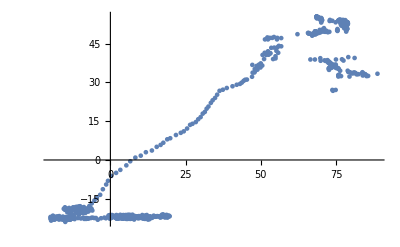

```mathematica
ListPlot[deltas]
```

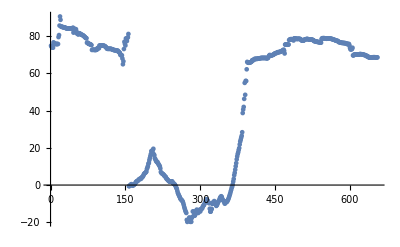

```mathematica
ListPlot[data[[All,5]] ]
```

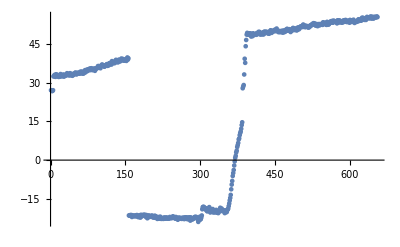

```mathematica
ListPlot[data[[All,6]] ]
```

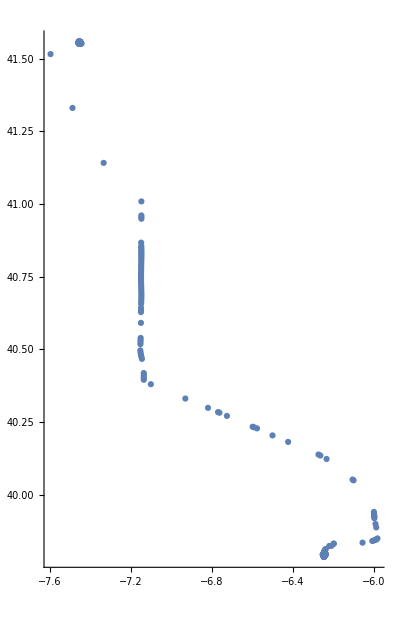

```mathematica
ListPlot[data[[All,3;;4]],AspectRatio-> 1.55]
```

```mathematica
data[[8]]
```

{1,600,-7.45,41.552,76.,33.0211}

```mathematica
q=Reverse[data[[10;;15]],2]
```

{{32.2695,75.8,41.5523,-7.4504,800,1},{33.2717,75.8,41.5524,-7.4504,900,1},{32.7706,75.8,41.5524,-7.4505,1000,1},{33.1046,75.8,41.5524,-7.4505,1100,1},{32.7706,75.8,41.5524,-7.4505,1200,1},{32.6871,75.8,41.5524,-7.4506,1300,1}}

```mathematica
Options[ListPointPlot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,Epilog→{},FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Automatic,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,Method→Automatic,Method→Automatic,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,SphericalRegion→False,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm,PlotTheme:>$PlotTheme}